```mathematica
Get["NeutronBeam/NBeam+ExB_Proton.m"]
```

```mathematica
xDetFTest=xDetF[0.,0.012,0.014,500000,Pi/4,Pi,0.2,1.,1.05,1.,1.,1.,0.95,0.,-15000.,0.]
```

0.0410594

```mathematica
yDetFTest=yDetF[0.,0.012,0.014,500000,Pi/4,Pi,0.2,1.,1.05,1.,1.,1.,0.95,0.,-15000.,0.]
```

0.0140175

```mathematica
yDVHandSolve[0.,xDetFTest,yDetFTest,500000,Pi/4,0.2,1.,1.05,0.95,0.,-15000,0.]
```

0.014

```mathematica
xDVHandSolve[0.,xDetFTest,yDetFTest,500000,Pi/4,Pi,0.2,1.,1.05,0.95,1.,1.,1.,0.,-15000,0.]
```

0.012

```mathematica
xDVHandSolve[0.,xDetFTest,yDetFTest,500000,Pi/4,Pi,0.2,1.,1.05,0.95,1.,1.,1.,0.,-15000,0.]
```

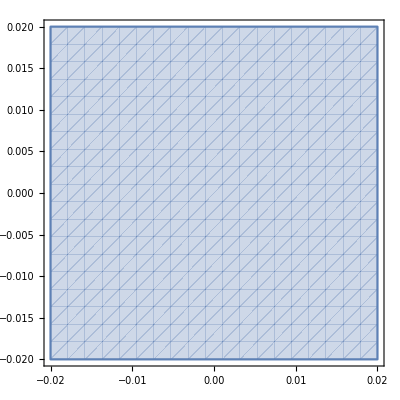

```mathematica
RegionPlot[
xDV==xDVHandSolve[0.,
xDetF[0.,xDV,yDV,500000,Pi/4,Pi,0.2,1.,1.05,1.,1.,1.,0.95,0.,-15000.,0.],
yDetF[0.,xDV,yDV,500000,Pi/4,Pi,0.2,1.,1.05,1.,1.,1.,0.95,0.,-15000.,0.],
500000,Pi/4,Pi,0.2,1.,1.05,0.95,1.,1.,1.,0.,-15000,0.]
&&
yDV==yDVHandSolve[0.,
xDetF[0.,xDV,yDV,500000,Pi/4,Pi,0.2,1.,1.05,1.,1.,1.,0.95,0.,-15000.,0.],
yDetF[0.,xDV,yDV,500000,Pi/4,Pi,0.2,1.,1.05,1.,1.,1.,0.95,0.,-15000.,0.],
500000,Pi/4,0.2,1.,1.05,0.95,0.,-15000,0.]
,{xDV,-0.02,0.02},{yDV,-0.02,0.02}]
```

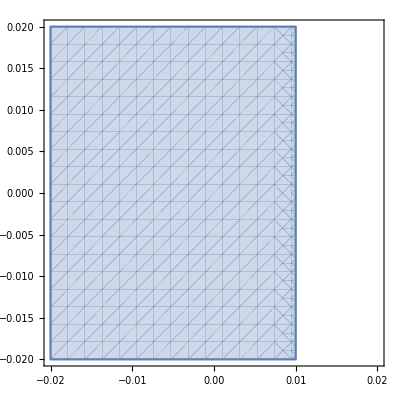

```mathematica
RegionPlot[x<0.01,{x,-0.02,0.02},{yDV,-0.02,0.02}]
```

```mathematica
IntegrandProton2DwNBeamAccelCompiled[λ0,a0,0.,0.,0.,{0.,0.,0.,500000.,Pi/4},{Pi,0.2,1.,1.05,1.,1.,1.,1.,0.,-15000.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.}]
```

0.0000996278

```mathematica
Plot3D[
IntegrandProton2DwNBeamAccelCompiled[λ0,a0,0.,0.,0.,{0.,phiA,0.,p,Pi/4},{Pi,0.2,1.,1.05,1.,1.,1.,1.,0.,-15000.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.}],
{p,0,ppmax},{phiA,-Pi,Pi}]
```

-Graphics3D-

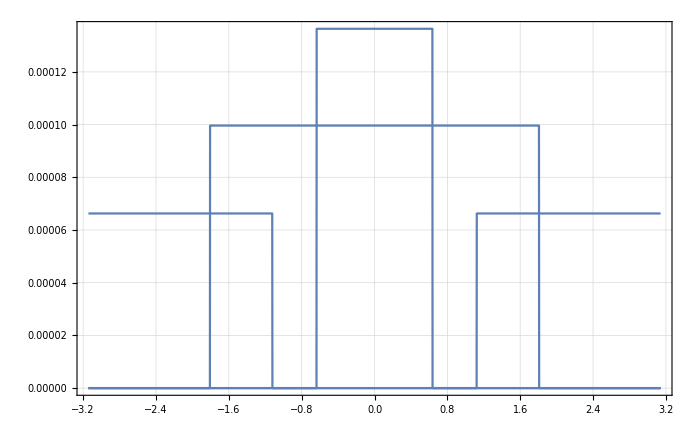

```mathematica
Plot[
Table[
IntegrandProton2DwNBeamAccelCompiled[λ0,a0,0.,0.,0.,{0.,phiA,0.,p,Pi/4},{Pi,0.2,1.,1.05,1.,1.,1.,1.,0.,-15000.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.}],{p,{3,4,5,6}*10^5}],
{phiA,-Pi,Pi}]
```

```mathematica
Solve[xOff+xAA/2==xAAccel[xGCVar,phiAlocal,plocal,th0,BRxB,rRxB,rA],phiAlocal][[All,1,2,1,1]]
```

{-ArcCos[(149896229 BRxB rA (xAA-2 xGCVar+2 xOff) Csc[th0])/(plocal rRxB)],ArcCos[(149896229 BRxB rA (xAA-2 xGCVar+2 xOff) Csc[th0])/(plocal rRxB)]}

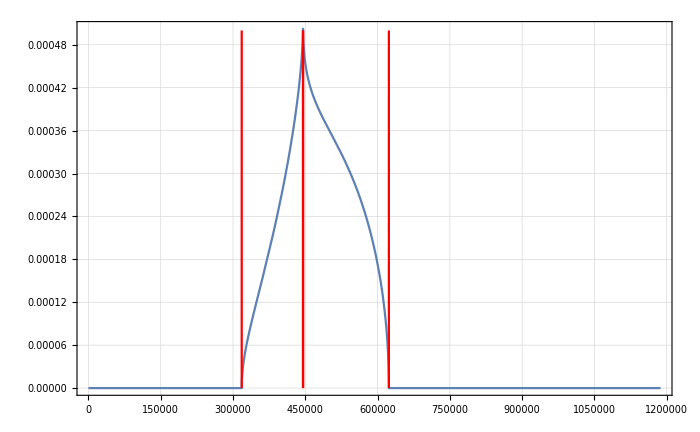

```mathematica
Show[
Plot[
ManualphiAIntegrandAllLimitsAccel[λ0,a0,0.,0.,0.,{0.,0.,p,Pi/4},{Pi,0.2,1.,1.05,1.,1.,1.,1.,0.,-15000.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.}],
{p,0,pmax},PlotPoints->60],
ParametricPlot[{
{pLimitsApertXListAccel[0.,0.,0.,Pi/4,Pi,0.2,1.,1.05,1.,0.,1,1,1,-0.03,0.01,0.,-15000][[1]],y},
{pLimitsApertXListAccel[0.,0.,0.,Pi/4,Pi,0.2,1.,1.05,1.,0.,1,1,1,-0.03,0.01,0.,-15000][[2]],y},
{pLimitsApertXListAccel[0.,0.,0.,Pi/4,Pi,0.2,1.,1.05,1.,0.,1,1,1,-0.03,0.01,0.,-15000][[3]],y},{pLimitsApertXListAccel[0.,0.,0.,Pi/4,Pi,0.2,1.,1.05,1.,0.,1,1,1,-0.03,0.01,0.,-15000][[4]],y}
},{y,0,0.0005},PlotStyle->Red]
]
```

```mathematica
xAAccel[xGCAF[xDVHandSolve[phiDV,xDet,yDet,plocal,th0,alpha,BRxB,rRxB,rA,rD,R,G1,G2,ExBscale,U,phiDet],phiDV,plocal,th0,BRxB,rRxB,rA],phiA,plocal,th0,BRxB,rRxB,rA]
```

(plocal rRxB Cos[phiA] Sin[th0])/(299792458 BRxB rA)+(xDet-(3.33564×10^-9 rRxB √(5.32894×10^-10 plocal^2-U) Cos[phiDet] √((plocal^2 rD Sin[th0]^2)/(5.32894×10^-10 plocal^2-U)))/(BRxB rD))/(√(rRxB/rD))+(ExBscale (20-5.47468×10^-6 plocal) rA (-(ExBscale (20-5.47468×10^-6 plocal) (xDet-(3.33564×10^-9 rRxB √(5.32894×10^-10 plocal^2-U) Cos[phiDet] √((plocal^2 rD Sin[th0]^2)/(5.32894×10^-10 plocal^2-U)))/(BRxB rD)))/(50 √(rRxB/rD))+(yDet-(3.33564×10^-9 rRxB √(5.32894×10^-10 plocal^2-U) Sin[phiDet] √((plocal^2 rD Sin[th0]^2)/(5.32894×10^-10 plocal^2-U)))/(BRxB rD))/(√(rRxB/rD))))/(50 (1+(ExBscale^2 (20-5.47468×10^-6 plocal)^2)/2500))-(alpha plocal (2-rRxB Sin[th0]^2))/(599584916 √(1-rRxB Sin[th0]^2) (BRxB-(BRxB G1 (-(ExBscale (20-5.47468×10^-6 plocal) (xDet-(3.33564×10^-9 rRxB √(5.32894×10^-10 plocal^2-U) Cos[phiDet] √((plocal^2 rD Sin[th0]^2)/(5.32894×10^-10 plocal^2-U)))/(BRxB rD)))/(50 √(rRxB/rD))+(yDet-(3.33564×10^-9 rRxB √(5.32894×10^-10 plocal^2-U) Sin[phiDet] √((plocal^2 rD Sin[th0]^2)/(5.32894×10^-10 plocal^2-U)))/(BRxB rD))/(√(rRxB/rD))))/((1+(ExBscale^2 (20-5.47468×10^-6 plocal)^2)/2500) R)+(BRxB G2 (-(ExBscale (20-5.47468×10^-6 plocal) (xDet-(3.33564×10^-9 rRxB √(5.32894×10^-10 plocal^2-U) Cos[phiDet] √((plocal^2 rD Sin[th0]^2)/(5.32894×10^-10 plocal^2-U)))/(BRxB rD)))/(50 √(rRxB/rD))+(yDet-(3.33564×10^-9 rRxB √(5.32894×10^-10 plocal^2-U) Sin[phiDet] √((plocal^2 rD Sin[th0]^2)/(5.32894×10^-10 plocal^2-U)))/(BRxB rD))/(√(rRxB/rD)))^2)/((1+(ExBscale^2 (20-5.47468×10^-6 plocal)^2)/2500)^2 R^2)))

```mathematica
?pLimitsApertXListAccel
```

```mathematica
pLimitsApertXListAccel[0.,0.,0.,Pi/4,Pi,0.2,1.,1.05,1.,0.,1,1,1,-0.03,0.01,0.,-15000]
```

{318068.,445296.,445346.,623485.}

```mathematica
pminApertAccel[0.,0,0.,0.,Pi/4,Pi,0.2,1.,1.05,1.,0.,1,1,1,-0.03,0.01,0.,-15000]
```

{445346.}

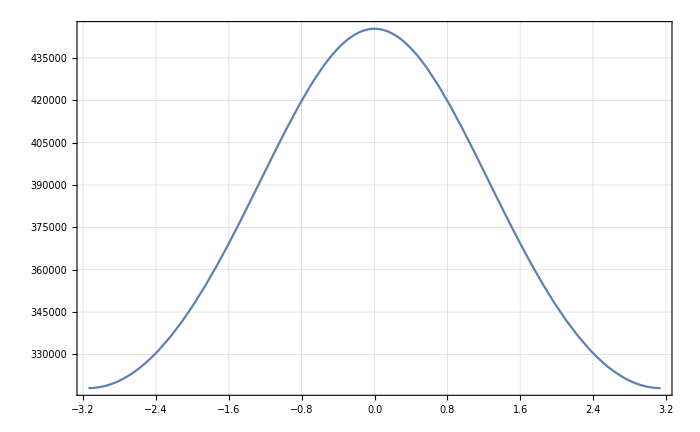

```mathematica
Plot[pminApertAccel[0.,phiA,0.,0.,Pi/4,Pi,0.2,1.,1.05,1.,0.,1,1,1,-0.03,0.01,0.,-15000],{phiA,-Pi,Pi}]
```

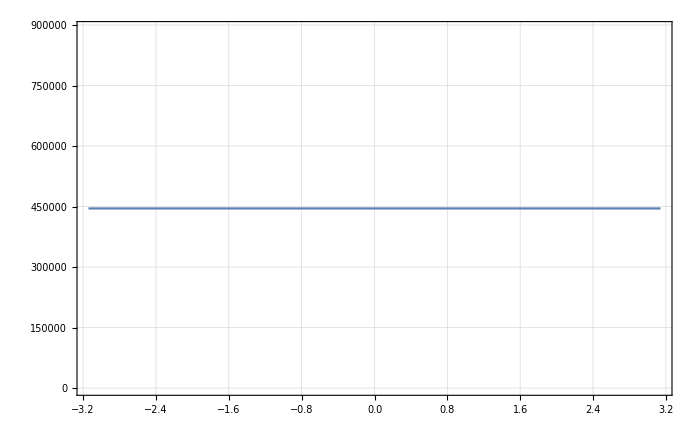

```mathematica
Plot[pminApertAccel[phiDV,0.,0.,0.,Pi/4,Pi,0.2,1.,1.05,1.,0.,1,1,1,-0.03,0.01,0.,-15000],{phiDV,-Pi,Pi}]
```

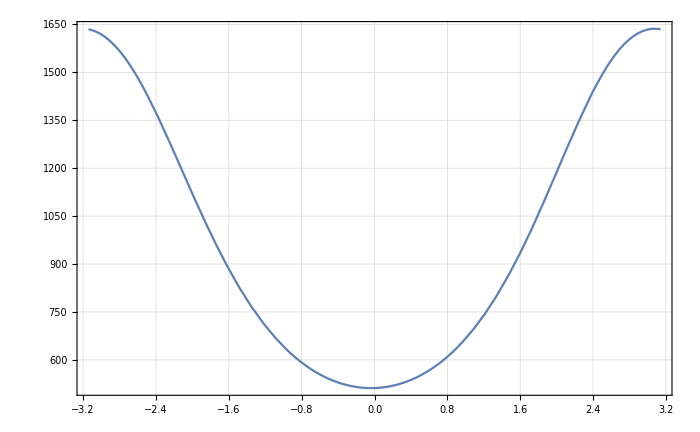

```mathematica
Plot[
Step1IntAccel[λ0,a0,0.,0.,0.,{phiDet,Pi/4},{Pi,0.2,1.,1.05,1.,1,1,1,0.,-15000},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},{"GlobalAdaptive",Method->"MultidimensionalRule"},3,3,0,2],{phiDet,-Pi,Pi}]
```